## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170608";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

## m1-m2 Plot, 22

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0385};
contourPD[p]={0.045};
contourPD[p]={0.032};
contourPD[p]={0.032};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 21950 + 镜像 21950

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.032}，共 2 条

第一条前3点：{{10.0165,10.3519},{9.91818,10.4583},{9.91805,10.4584}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.508867

可信水平百分比：50.8867%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.508867

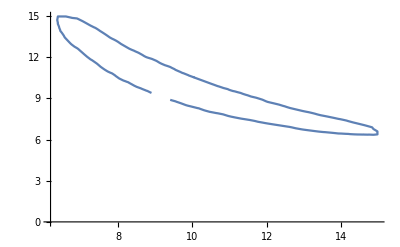

```mathematica
ListLinePlot[mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]]
```

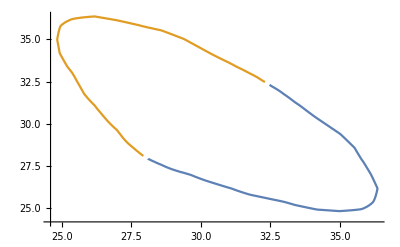

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

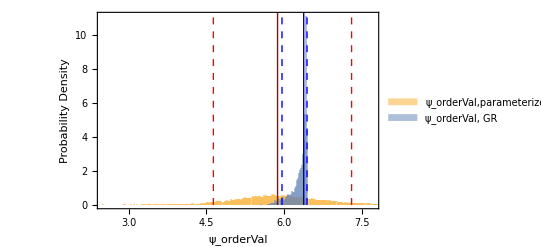

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
evolPlots=<||>
```

<||>

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.294083, 0.705917}

实际使用的 GR 概率区间上下界: {6.2852, 6.42201}

实际使用的 Param 概率区间上下界: {5.46979, 6.3035}

GR下界: 点数=1100 | Y>0点数=1100 | 平均误差=8.98675×10^-16

GR上界: 点数=1100 | Y>0点数=1100 | 平均误差=8.0905×10^-16

Param下界: 点数=1100 | Y>0点数=1100 | 平均误差=1.58257×10^-16

Param上界: 点数=1100 | Y>0点数=1100 | 平均误差=1.03755×10^-15

{{5.01,44.505},{5.02,44.5939},{5.03,44.6827},{5.04,44.7715},{5.05,44.8604}}

{{5.01,9.32208},{5.02,9.34068},{5.03,9.35929},{5.04,9.3779},{5.05,9.3965}}

chi1L取值：0.367177

chi2L取值：0.405346

=====================================================

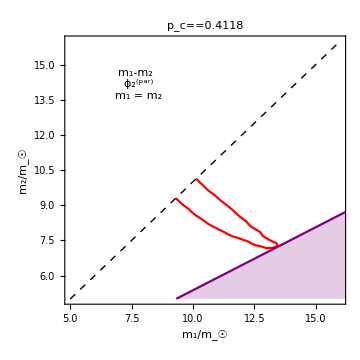

```mathematica
probability=prob;
(*probability=0.37;*)

evolPlots["at"]=PlotInversion[p,probability,5,16,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.340103, 0.659897}

实际使用的 GR 概率区间上下界: {6.30971, 6.41479}

实际使用的 Param 概率区间上下界: {5.56542, 6.192}

GR下界: 点数=1100 | Y>0点数=1100 | 平均误差=1.21115×10^-16

GR上界: 点数=1100 | Y>0点数=1100 | 平均误差=5.56323×10^-16

Param下界: 点数=1100 | Y>0点数=1100 | 平均误差=7.86442×10^-16

Param上界: 点数=1100 | Y>0点数=1100 | 平均误差=1.17563×10^-15

{{5.01,36.29},{5.02,36.3625},{5.03,36.4349},{5.04,36.5073},{5.05,36.5798}}

{{5.01,11.8121},{5.02,11.8357},{5.03,11.8593},{5.04,11.8828},{5.05,11.9064}}

chi1L取值：0.367177

chi2L取值：0.405346

=====================================================

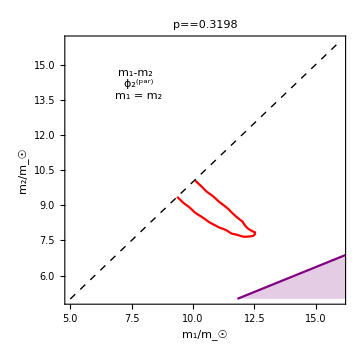

```mathematica
probability=prob;
(*probability=0.33*)

evolPlots["before"]=PlotInversion[p,probability,5,16,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.245567, 0.754433}

实际使用的 GR 概率区间上下界: {6.25357, 6.42799}

实际使用的 Param 概率区间上下界: {5.36586, 6.42889}

GR下界: 点数=1100 | Y>0点数=1100 | 平均误差=7.54144×10^-16

GR上界: 点数=1100 | Y>0点数=1100 | 平均误差=4.69927×10^-16

Param下界: 点数=1100 | Y>0点数=1100 | 平均误差=1.12395×10^-15

Param上界: 点数=1100 | Y>0点数=1100 | 平均误差=5.32907×10^-16

{{5.01,57.302},{5.02,57.4164},{5.03,57.5308},{5.04,57.6451},{5.05,57.7595}}

{{5.01,6.02437},{5.02,6.0364},{5.03,6.04842},{5.04,6.06044},{5.05,6.07247}}

chi1L取值：0.367177

chi2L取值：0.405346

=====================================================

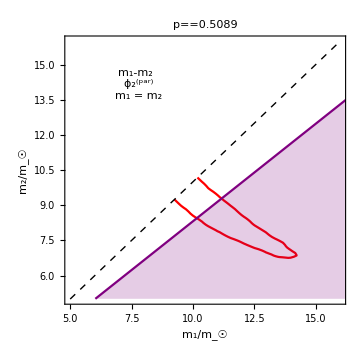

```mathematica
probability=prob;
(*probability=0.5;*)

evolPlots["after"]=PlotInversion[p,probability,5,16,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_dphi2_"<>key<>".pdf"}],evolPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[evolPlots]}]
```

正在导出矢量图: plot_at.pdf ...

正在导出矢量图: plot_before.pdf ...

正在导出矢量图: plot_after.pdf ...

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0389};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 16716 + 镜像 16716

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0389}，共 2 条

第一条前3点：{{10.2419,9.73845},{10.2556,9.73095},{10.2897,9.71347}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.345422

可信水平百分比：34.5422%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.345422

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

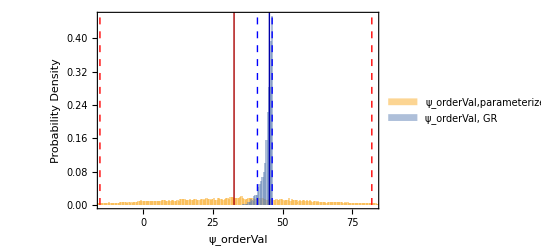

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.327289, 0.672711}

实际使用的 GR 概率区间上下界: {44.5102, 45.7747}

实际使用的 Param 概率区间上下界: {20.2029, 44.4067}

GR下界: 点数=17 | 平均误差=5.85153×10^-15

GR上界: 点数=17 | 平均误差=6.68746×10^-15

Param下界: 点数=17 | 平均误差=9.90038

Param上界: 点数=17 | 平均误差=4.59763×10^-15

chi1L取值：0.37315

chi2L取值：0.473781

=====================================================

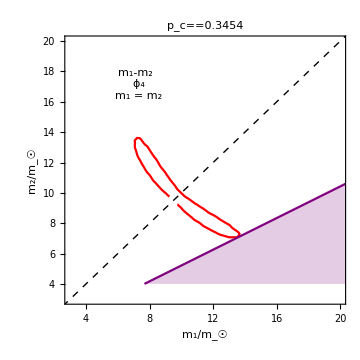

```mathematica
probability=prob;
(*probability=0.35;*)

PlotInversion[p,probability,3,20,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0595};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 19084 + 镜像 19084

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.0595}，共 2 条

第一条前3点：{{10.2003,9.86486},{10.2751,9.78846},{10.3016,9.76138}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.284669

可信水平百分比：28.4669%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.284669

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

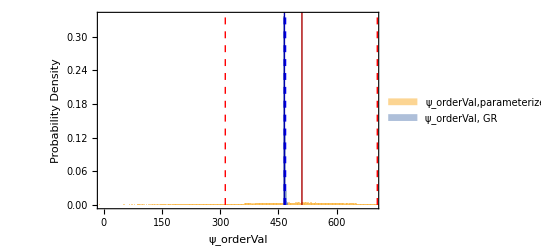

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.357665, 0.642335}

实际使用的 GR 概率区间上下界: {465.069, 465.883}

实际使用的 Param 概率区间上下界: {465.743, 552.978}

GR下界: 点数=170 | 平均误差=5.75122×10^-14

GR上界: 点数=170 | 平均误差=3.6781×10^-15

Param下界: 点数=170 | 平均误差=5.85153×10^-14

Param上界: 点数=170 | 平均误差=71.2055

chi1L取值：0.356536

chi2L取值：0.434395

=====================================================

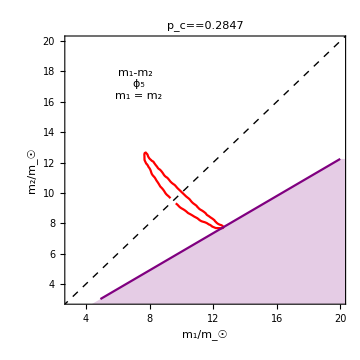

```mathematica
probability=prob;
(*probability=0.25;*)

PlotInversion[p,probability,3,20,0.1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0567};
contourPD[p]={0.065};
(*contourPD[p]={0.0535};*)
contourPD[p]={0.07};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 19299 + 镜像 19299

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.07}，共 2 条

第一条前3点：{{9.86104,9.52663},{10.0405,9.55801},{9.93006,9.59565}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.00404851

可信水平百分比：0.404851%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.00404851

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

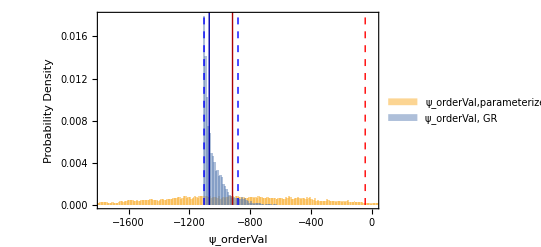

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.393952, 0.606048}

实际使用的 GR 概率区间上下界: {-1082.85, -1051.16}

实际使用的 Param 概率区间上下界: {-1069.31, -767.362}

GR下界: 点数=170 | 平均误差=1.39099×10^-13

GR上界: 点数=170 | 平均误差=1.20374×10^-13

Param下界: 点数=170 | 平均误差=1.17699×10^-13

Param上界: 点数=170 | 平均误差=1.21712×10^-13

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

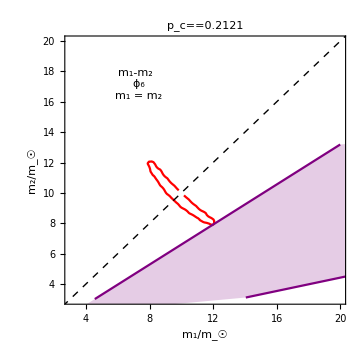

```mathematica
probability=prob;
(*probability=0.1;
*)
PlotInversion[p,probability,3,20,0.1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

```mathematica
evolPlots=<||>
```

<||>

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.393952, 0.606048}

实际使用的 GR 概率区间上下界: {-1082.85, -1051.16}

实际使用的 Param 概率区间上下界: {-1069.31, -767.362}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.50468×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.42309×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.09541×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.21177×10^-13

{{3.01,1.9847},{3.02,1.9913},{3.03,1.99789},{3.04,2.00448},{3.05,2.01108}}

{{3.01,13.649},{3.02,13.6943},{3.03,13.7397},{3.04,13.785},{3.05,13.8303}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

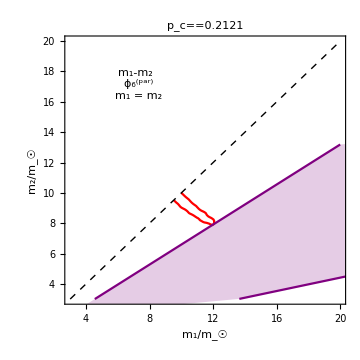

```mathematica
probability=prob;
(*probability=0.37;*)

evolPlots["at"]=PlotInversion[p,probability,3,20,0.01,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.46195, 0.53805}

实际使用的 GR 概率区间上下界: {-1074.97, -1064.26}

实际使用的 Param 概率区间上下界: {-967.28, -866.719}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.40303×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=7.77083×10^-14

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.59028×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.13018×10^-13

{{3.01,7.1425},{3.02,7.16623},{3.03,7.18996},{3.04,7.21369},{3.05,7.23741}}

{{3.01,9.96911},{3.02,10.0022},{3.03,10.0354},{3.04,10.0685},{3.05,10.1016}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

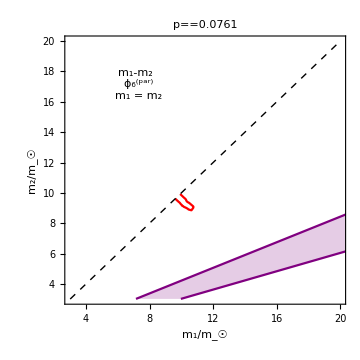

```mathematica
probability=prob;
(*probability=0.26;*)

evolPlots["before"]=PlotInversion[p,probability,3,20,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.368061, 0.631939}

实际使用的 GR 概率区间上下界: {-1085.85, -1045.8}

实际使用的 Param 概率区间上下界: {-1102.63, -730.851}

GR下界: 点数=2500 | Y>0点数=2500 | 平均误差=1.12414×10^-13

GR上界: 点数=2500 | Y>0点数=2500 | 平均误差=8.8221×10^-14

Param下界: 点数=2500 | Y>0点数=2500 | 平均误差=1.57888×10^-13

Param上界: 点数=2500 | Y>0点数=2500 | 平均误差=4.69754×10^-14

{{5.01,5.45459},{5.02,5.46548},{5.03,5.47636},{5.04,5.48725},{5.05,5.49814}}

{{5.01,25.5734},{5.02,25.6245},{5.03,25.6755},{5.04,25.7266},{5.05,25.7776}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

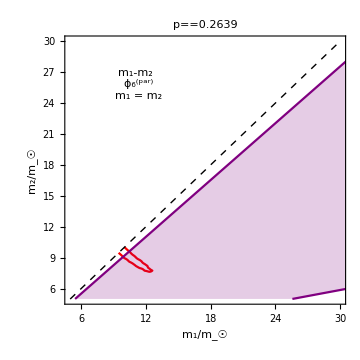

```mathematica
probability=prob;
(*probability=0.5;*)

evolPlots["after"]=PlotInversion[p,probability,5,30,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_dphi6_"<>key<>".pdf"}],evolPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[evolPlots]}]
```

正在导出矢量图: plot_at.pdf ...

正在导出矢量图: plot_before.pdf ...

正在导出矢量图: plot_after.pdf ...

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,20},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];


contourPD[p]={0.0722};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];
```

输入Mc范围：{3,20}

输入q范围：{1,3}

m1范围：{3.4461,40.9535}

m2范围：{2.04767,22.974}

对称数据：原始 19299 + 镜像 19299

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 40.9535} × {2.04767, 40.9535}

等高线值：{0.0722}，共 2 条

第一条前3点：{{9.44055,10.0769},{9.48938,10.1029},{9.51753,10.114}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.00630729

可信水平百分比：0.630729%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.00630729

```mathematica
NMaximize[{m1m2PDF[p][x,y],5<x<20&&5<y<20},{x,y}]
```

{10.0388,9.58097}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.5, 0.5}

实际使用的 GR 概率区间上下界: {-1069.58, -1069.58}

实际使用的 Param 概率区间上下界: {-916.268, -916.268}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.55818×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.55818×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.3736×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.3736×10^-13

{{3.01,8.49909},{3.02,8.52733},{3.03,8.55556},{3.04,8.5838},{3.05,8.61203}}

{{3.01,8.49909},{3.02,8.52733},{3.03,8.55556},{3.04,8.5838},{3.05,8.61203}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

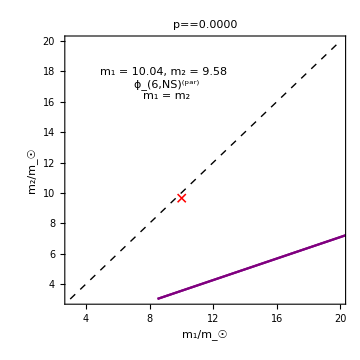

```mathematica
probability=prob;
probability=0.0;

{m1M,m2M}={10.038784221855547,9.580967992154612}

plotp0=PlotInversion[p,probability,3,20,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,
extremePoints->{{m1M,m2M}},extremePointsMarker->"Cross",extremePointsLegend->Row[{Subscript[Style["m",Italic],1]," = 10.04, ",Subscript[Style["m",Italic],2]," = 9.58"}]
,
labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];


Export[FileNameJoin[{targetDir,eventID<>"_dphi6_"<>"pzero"<>".pdf"}],plotp0,"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500]
```

D:\Documents\workspace\课题\论文\fig\GW170608\GW170608_dphi6_pzero.pdf

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.06};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 18147 + 镜像 18147

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.06}，共 2 条

第一条前3点：{{9.76043,9.42503},{9.81073,9.38484},{9.87235,9.33211}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.113927

可信水平百分比：11.3927%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.113927

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

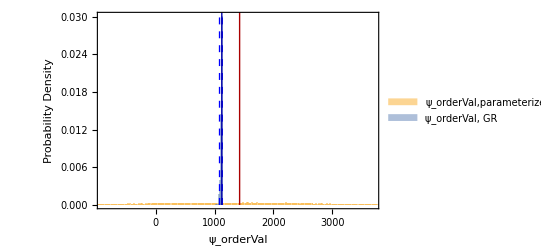

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
0.2927/2
```

0.14635

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4268, 0.5732}

实际使用的 GR 概率区间上下界: {1121.22, 1125.86}

实际使用的 Param 概率区间上下界: {1130.7, 1679.35}

GR下界: 点数=270 | 平均误差=3.87377×10^-14

GR上界: 点数=270 | 平均误差=4.96854×10^-14

Param下界: 点数=270 | 平均误差=3.45271×10^-14

Param上界: 点数=270 | 平均误差=548.456

chi1L取值：0.365235

chi2L取值：0.434549

=====================================================

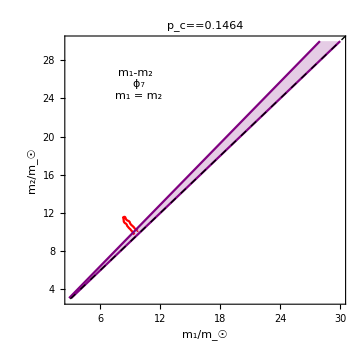

```mathematica
probability=prob;
probability=0.1464;
(*0.32*)
PlotInversion[p,probability,3,30,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 19613 + 镜像 19613

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.01}，共 2 条

第一条前3点：{{10.2051,10.7074},{10.206,10.7094},{10.1467,10.7921}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.844964

可信水平百分比：84.4964%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.844964

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

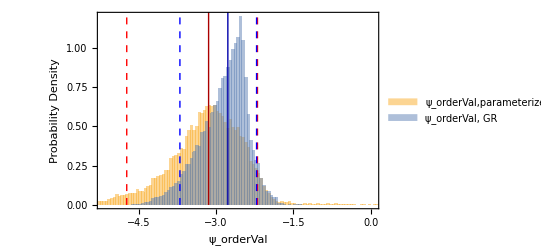

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
4034/2
```

2017

```mathematica
probability=prob;
probability=0.2014;

PlotInversion[p,probability,3,30,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.3993, 0.6007}

实际使用的 GR 概率区间上下界: {-2.89455, -2.66454}

实际使用的 Param 概率区间上下界: {-3.312, -2.98507}

GR下界: 点数=270 | 平均误差=1.56418×10^-15

GR上界: 点数=270 | 平均误差=1.27635×10^-15

Param下界: 点数=270 | 平均误差=0.017939

Param上界: 点数=270 | 平均误差=5.01656×10^-15

chi1L取值：0.331684

chi2L取值：0.391222

=====================================================

-Graphics-

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.02};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 21254 + 镜像 21254

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.02}，共 2 条

第一条前3点：{{8.92768,9.43109},{8.91033,9.4459},{8.7853,9.58411}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.753714

可信水平百分比：75.3714%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.753714

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

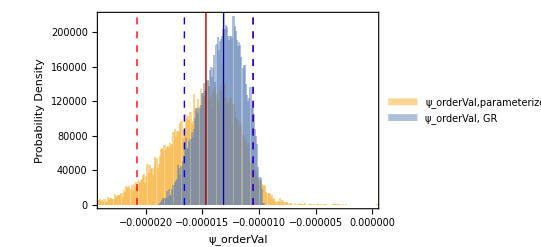

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.3579;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,100,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.32105, 0.67895}

实际使用的 GR 概率区间上下界: {-0.0000141181, -0.000012226}

实际使用的 Param 概率区间上下界: {-0.0000162698, -0.0000133003}

GR下界: 点数=97 | 平均误差=3.56278×10^-21

GR上界: 点数=97 | 平均误差=1.64167×10^-21

Param下界: 点数=97 | 平均误差=8.90621×10^-21

Param上界: 点数=97 | 平均误差=4.03432×10^-21

chi1L取值：0.337847

chi2L取值：0.430621

=====================================================

-Graphics-

# Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.005};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 27748 + 镜像 27748

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.005}，共 2 条

第一条前3点：{{9.31921,8.81676},{9.31755,8.81415},{9.33858,8.80187}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.949818

可信水平百分比：94.9818%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.949818

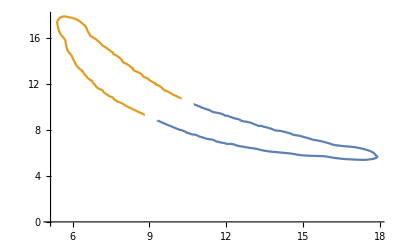

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

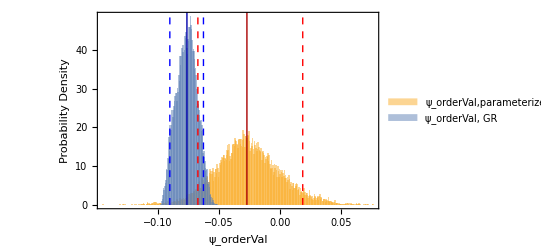

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.1984;

PlotInversion[p,probability,3,60,0.1,cm->True,cd->True,cu->False,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4008, 0.5992}

实际使用的 GR 概率区间上下界: {-0.0654034, -0.0614175}

实际使用的 Param 概率区间上下界: {-1.41995, -0.065961}

GR下界: 点数=570 | Y>0点数=570 | 平均误差=2.8486×10^-17

GR上界: 点数=570 | Y>0点数=570 | 平均误差=2.98129×10^-17

Greater::nord: Invalid comparison with -2.47304+1.99774 ⅈ attempted.

Greater::nord: Invalid comparison with -2.54798+2.05827 ⅈ attempted.

Greater::nord: Invalid comparison with -2.62292+2.11881 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param下界: 点数=570 | Y>0点数=2 | 平均误差=0.00475077

Param上界: 点数=570 | Y>0点数=570 | 平均误差=4.01969×10^-17

{{3.1,3.1},{3.2,3.2},{3.3,-2.47304+1.99774 ⅈ},{3.4,-2.54798+2.05827 ⅈ},{3.5,-2.62292+2.11881 ⅈ}}

{{3.1,3.04534},{3.2,3.14358},{3.3,3.24182},{3.4,3.34005},{3.5,3.43829}}

chi1L取值：0.28881

chi2L取值：0.424911

=====================================================

-Graphics-

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.40085, 0.59915}

实际使用的 GR 概率区间上下界: {-0.0654033, -0.0614177}

实际使用的 Param 概率区间上下界: {-1.4199, -0.06601}

GR下界: 点数=570 | Y>0点数=570 | 平均误差=1.87472×10^-17

GR上界: 点数=570 | Y>0点数=570 | 平均误差=1.39143×10^-17

Param下界: 点数=570 | Y>0点数=570 | 平均误差=1.35241

Param上界: 点数=570 | Y>0点数=570 | 平均误差=2.13523×10^-17

{{3.1,4.1976},{3.2,4.32865},{3.3,4.46302},{3.4,4.6008},{3.5,4.73526}}

{{3.1,6.43108},{3.2,6.63853},{3.3,6.84598},{3.4,7.05344},{3.5,7.26089}}

chi1L取值：0.646707

chi2L取值：0.102665

=====================================================

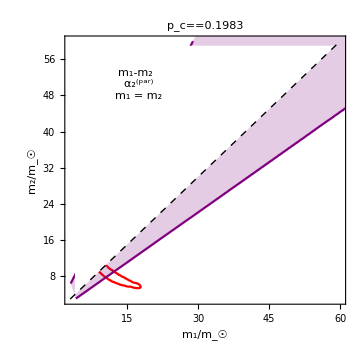

```mathematica
probability=prob;
probability=0.1983;

PlotInversion[p,probability,3,60,0.1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.9,spinPercentile2->0.1,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,30},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.05865};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：5 (合并模式: False)

区域内总积分值：0.058533

可信水平百分比：5.8533%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.058533

输入Mc范围：{3,30}

输入q范围：{1,5}

m1范围：{3.4461,81.7221}

m2范围：{1.63444,34.461}

对称数据：原始 18861 + 镜像 18861

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 81.7221} × {1.63444, 81.7221}

等高线值：{0.05865}，共 3 条

第一条前3点：{{11.5715,8.49428},{11.4921,8.53583},{11.4438,8.56606}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：3 (合并模式: False)

区域内总积分值：0.0509786

可信水平百分比：5.09786%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.0509786

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

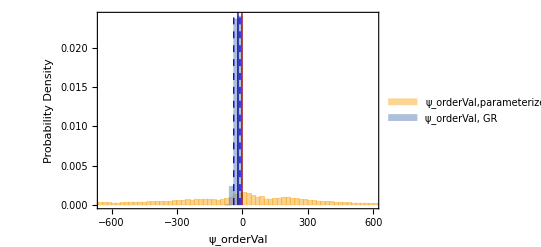

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.474511, 0.525489}

实际使用的 GR 概率区间上下界: {-20.8982, -19.9018}

实际使用的 Param 概率区间上下界: {-19.3024, 14.6439}

GR下界: 点数=170 | 平均误差=3.70318×10^-14

GR上界: 点数=170 | 平均误差=3.14729×10^-14

Param下界: 点数=170 | 平均误差=3.18072×10^-14

Param上界: 点数=170 | 平均误差=6.93784

chi1L取值：0.366219

chi2L取值：0.431106

=====================================================

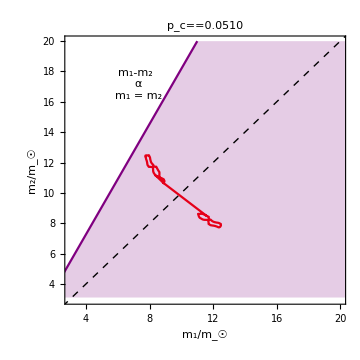

```mathematica
probability=prob;
(*probability=0.06;
*)
PlotInversion[p,probability,3,20,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2,3}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,20},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0809};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False ][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,20}

输入q范围：{1,5}

m1范围：{3.4461,54.4814}

m2范围：{1.63444,22.974}

对称数据：原始 26622 + 镜像 26622

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 54.4814} × {1.63444, 54.4814}

等高线值：{0.0809}，共 2 条

第一条前3点：{{9.66422,9.49922},{9.66429,9.49914},{9.68175,9.4843}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.188067

可信水平百分比：18.8067%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.188067

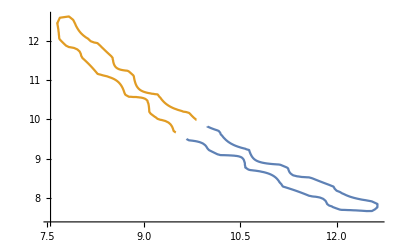

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

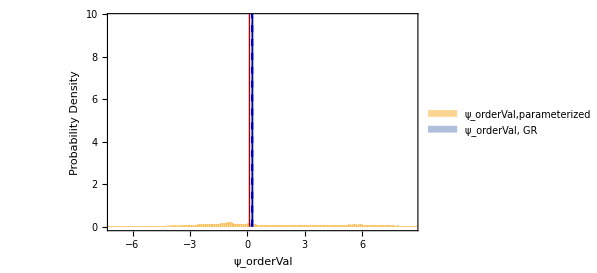

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.495, 0.505}

实际使用的 GR 概率区间上下界: {0.258657, 0.258998}

实际使用的 Param 概率区间上下界: {0.0703116, 0.156723}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=3.68986×10^-17

GR上界: 点数=170 | Y>0点数=170 | 平均误差=3.46128×10^-17

Param下界: 点数=170 | Y>0点数=170 | 平均误差=1.07757×10^-17

Param上界: 点数=170 | Y>0点数=170 | 平均误差=3.05311×10^-17

{{3.1,39.7802},{3.2,41.0634},{3.3,42.3467},{3.4,43.6299},{3.5,44.9131}}

{{3.1,14.0641},{3.2,14.5178},{3.3,14.9715},{3.4,15.4252},{3.5,15.8788}}

chi1L取值：0.303163

chi2L取值：0.384705

=====================================================

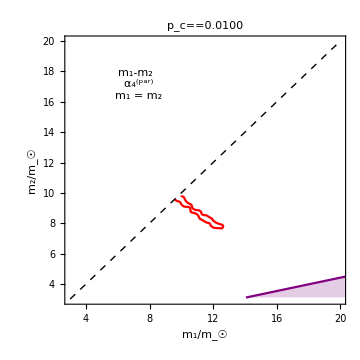

=====================================================

chi2L取值：0.384705

chi1L取值：0.303163

Param上界: 点数=170 | 平均误差=5.74704×10^-17

Param下界: 点数=170 | 平均误差=0.0130508

GR上界: 点数=170 | 平均误差=6.7593×10^-17

GR下界: 点数=170 | 平均误差=4.14701×10^-17

实际使用的 Param 概率区间上下界: {-0.0134924, 0.250581}

实际使用的 GR 概率区间上下界: {0.258358, 0.259322}

实际使用的概率区间上下界: {0.485, 0.515}

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.485, 0.515}

实际使用的 GR 概率区间上下界: {0.258358, 0.259322}

实际使用的 Param 概率区间上下界: {-0.0134924, 0.250581}

GR下界: 点数=170 | 平均误差=4.14701×10^-17

GR上界: 点数=170 | 平均误差=6.7593×10^-17

Param下界: 点数=170 | 平均误差=0.0130508

Param上界: 点数=170 | 平均误差=5.74704×10^-17

chi1L取值：0.303163

chi2L取值：0.384705

=====================================================

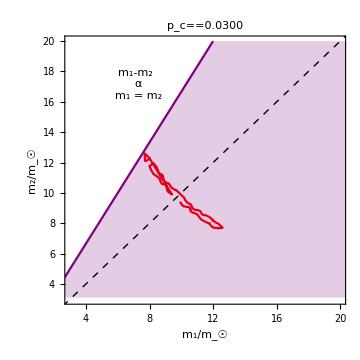

```mathematica
probability=prob;
probability=0.01;

PlotInversion[p,probability,3,20,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

```mathematica
p
```

dalpha_4

# utils